# GH, SHEL and OIF Shifts: Single Interface M. T. Lusk Last Edited: August 30, 2016

-Graphics-

## Applications

### Generate Gaussian Beam

```mathematica
Clear[Escalar,r,φfunc,z,w,w0,zR,λ,k,R,ψ,Nmax,Evec,k0];

ω = c1 k0;

r[x_,y_]=Sqrt[x^2+y^2];
φfunc[x_,y_]=ArcTan[x,y];

λ = 2 π/k0;

zR = π w0^2/λ;

w[z_]=w0 √(1+(z/zR)^2);

R[z_]=Simplify[z(1 + (zR/z)^2)];

Nmax = 2 p+Abs[ℓ];

ψ[z_]=(Nmax+1)ArcTan[zR,z];


Escalar[x_,y_,z_]=Simplify[1/w[z] Exp[(-(x^2+y^2))/w[z]^2]Exp[-ⅈ (k0 (x^2+y^2)/(2 R[z])+ k0 z+ψ[z])]((r[x,y] √2)/w[z])^Abs[ℓ] LaguerreL[p,Abs[ℓ],(2(x^2+y^2))/w[z]^2]Exp[-ⅈ ℓ φfunc[x,y]],{Element[x,Reals],Element[y,Reals],Element[z,Reals]}];
```

```mathematica
Escalar2D[x_,y_]=FullSimplify[Escalar[x,y,0],{k0>0,w0>0}] /. w0 ->wk/k0(*wk is its own variable! It makes things look like only k is squared*)
```

(2^(Abs[ℓ]/2) ⅇ^(-(k0^2 (x^2+y^2))/wk^2-ⅈ ℓ ArcTan[x,y]) k0 (k0/(wk √(1/(x^2+y^2))))^Abs[ℓ] LaguerreL[p,Abs[ℓ],(2 k0^2 (x^2+y^2))/wk^2])/wk

### Define Vecs (κvec , κvec0, nvec)

```mathematica
Clear[κvec,κx,κy,κz];

κvec = {κx ,κy,√(1-κx^2-κy^2)};

κvec0 = {0,0,1};

nvec = {-Sin[θ],0,Cos[θ]};
```

### Fresnel Coefficients

```mathematica
Clear[R1,R2,β,n];

β =ArcCos[κvec.nvec];

R2=(Cos[β]-√(n^2-Sin[β]^2))/(Cos[β]+√(n^2-Sin[β]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1=(n^2 Cos[β]-√(n^2-Sin[β]^2))/(n^2 Cos[β]+√(n^2-Sin[β]^2));(* Fresnel Reflection Coefficient: p/TM *)

T2=Simplify[(2Cos[β])/(Cos[β]+√(n^2-Sin[β]^2))];(* Fresnel Transmission Coefficient: s/TE *)

T1=Simplify[(2n Cos[β])/(n^2 Cos[β]+√(n^2-Sin[β]^2))];(* Fresnel Transmission Coefficient: p/TM *)
R2/.{n->.659,θ->30Degree,κx->0,κy->0}
R1/.{n->.659,θ->30Degree,κx->0,κy->0}
T2/.{n->.659,θ->30Degree,κx->0,κy->0}
T1/.{n->.659,θ->30Degree,κx->0,κy->0}
```

0.337176

-0.0660327

1.33718

1.41725

### Centroid Shifts versus Angle of Incidence: n = 1/1.5168, OAM = 0 (Glass/Air) FIG 4

#### Analysis: DON’T RUN THIS. It takes too long

```mathematica
Clear[plots,k0];

fontset = 6;

IFshift$tab$R1 = {};
IFshift$tab$R2 = {};
IFshift$tab$R3 = {};
IFshift$tab$R4 = {};
IFshift$tab$T1 = {};
IFshift$tab$T2 = {};
IFshift$tab$T3 = {};
IFshift$tab$T4 = {};

λ0 = 2 π;

dimset = 11;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)
dimset = 11;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
small = π*10^-10;

Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;

κtab= Table[{κperp[i],κperp[j],√(1-κperp[i]^2-κperp[j]^2)},{j,1,dimset},{i,1,dimset}];
κtab= Table[{κperp[i],κperp[j],1},{j,1,dimset},{i,1,dimset}];

params$here = {wk->20.,n->1/1.5168,θ->60 Degree,k0->1,p->0,ℓ->0};

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}] (*Some Values are too small for cpp*);

E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}](*The Fourier Command Scales the output By dimset (CPP scales it by dimset^2 and has the opposite sign in the imaginary)*);
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)

f = {1,0,0};

θR=π-θ /. params$here;

eR = {(f[[1]]R1-f[[2]]κy Cot[θ](R1+R2)),f[[2]]R2 + f[[1]]κy Cot[θ](R1+R2 ),-(f[[1]]R1 κx + f[[2]]R2  κy)} /. params$here;

eRtab = Table[eR /. {κx->κtab[[i,j]][[1]],κy->κtab[[i,j]][[2]]}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];
ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

IFshift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];
IFshift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];
```

#### 2-D Beam Testing

```mathematica
test =Table[ⅇ^((-k0(x^2+y^2))/wk)/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];Table[(-k0(x^2+y^2))/wk/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
Table[Re[Etab[[x,y]]],{y,1,dimset},{x,1,dimset}]//MatrixForm;
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Etab;
test;
```

#### Plane Wave Analysis

```mathematica
Etab = Table[1+ⅈ/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}] (*Some Values are too small for cpp*);
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
MatrixForm[Etab]
Fourier[Etab]/11//MatrixForm
MatrixForm[E$tilde]
Chop[E$tilde]//MatrixForm
InverseFourier[RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}]]//MatrixForm
```

(1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ
1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ
1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ
1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ
1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ
1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ
1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ
1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ
1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ
1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ
1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ | 1+ⅈ)

(1.+1. ⅈ | -1.00929×10^-17-1.00929×10^-17 ⅈ | -2.01859×10^-17-2.01859×10^-17 ⅈ | -2.01859×10^-17-2.01859×10^-17 ⅈ | -3.53253×10^-17-3.53253×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -3.53253×10^-17-3.53253×10^-17 ⅈ | -2.01859×10^-17-2.01859×10^-17 ⅈ | -2.01859×10^-17-2.01859×10^-17 ⅈ | -1.00929×10^-17-1.00929×10^-17 ⅈ
-1.46806×10^-17-1.46806×10^-17 ⅈ | 1.01867×10^-34+1.01867×10^-34 ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ | -8.14939×10^-34-8.14939×10^-34 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -8.14939×10^-34-8.14939×10^-34 ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ | 1.01867×10^-34+1.01867×10^-34 ⅈ
-1.46806×10^-17-1.46806×10^-17 ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ
0.+0. ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ
-1.83508×10^-17-1.83508×10^-17 ⅈ | 3.56536×10^-34+3.56536×10^-34 ⅈ | 7.13072×10^-34+7.13072×10^-34 ⅈ | 7.13072×10^-34+7.13072×10^-34 ⅈ | -1.01867×10^-34-1.01867×10^-34 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.01867×10^-34-1.01867×10^-34 ⅈ | 7.13072×10^-34+7.13072×10^-34 ⅈ | 7.13072×10^-34+7.13072×10^-34 ⅈ | 3.56536×10^-34+3.56536×10^-34 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.83508×10^-17-1.83508×10^-17 ⅈ | 3.56536×10^-34+3.56536×10^-34 ⅈ | 7.13072×10^-34+7.13072×10^-34 ⅈ | 7.13072×10^-34+7.13072×10^-34 ⅈ | -1.01867×10^-34-1.01867×10^-34 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.01867×10^-34-1.01867×10^-34 ⅈ | 7.13072×10^-34+7.13072×10^-34 ⅈ | 7.13072×10^-34+7.13072×10^-34 ⅈ | 3.56536×10^-34+3.56536×10^-34 ⅈ
0.+0. ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ
-1.46806×10^-17-1.46806×10^-17 ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 4.07469×10^-34+4.07469×10^-34 ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ
-1.46806×10^-17-1.46806×10^-17 ⅈ | 1.01867×10^-34+1.01867×10^-34 ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ | -8.14939×10^-34-8.14939×10^-34 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -8.14939×10^-34-8.14939×10^-34 ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ | 2.03735×10^-34+2.03735×10^-34 ⅈ | 1.01867×10^-34+1.01867×10^-34 ⅈ)

(0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -1.12054×10^-33-1.12054×10^-33 ⅈ | 7.84379×10^-33+7.84379×10^-33 ⅈ | 7.84379×10^-33+7.84379×10^-33 ⅈ | 3.92189×10^-33+3.92189×10^-33 ⅈ | -2.01859×10^-16-2.01859×10^-16 ⅈ | 3.92189×10^-33+3.92189×10^-33 ⅈ | 7.84379×10^-33+7.84379×10^-33 ⅈ | 7.84379×10^-33+7.84379×10^-33 ⅈ | -1.12054×10^-33-1.12054×10^-33 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | 0.+0. ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | -1.61487×10^-16-1.61487×10^-16 ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -8.96433×10^-33-8.96433×10^-33 ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | 1.12054×10^-33+1.12054×10^-33 ⅈ | -1.61487×10^-16-1.61487×10^-16 ⅈ | 1.12054×10^-33+1.12054×10^-33 ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | -8.96433×10^-33-8.96433×10^-33 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -3.88578×10^-16-3.88578×10^-16 ⅈ | -2.22045×10^-16-2.22045×10^-16 ⅈ | -2.22045×10^-16-2.22045×10^-16 ⅈ | -1.11022×10^-16-1.11022×10^-16 ⅈ | 11.+11. ⅈ | -1.11022×10^-16-1.11022×10^-16 ⅈ | -2.22045×10^-16-2.22045×10^-16 ⅈ | -2.22045×10^-16-2.22045×10^-16 ⅈ | -3.88578×10^-16-3.88578×10^-16 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -8.96433×10^-33-8.96433×10^-33 ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | 1.12054×10^-33+1.12054×10^-33 ⅈ | -1.61487×10^-16-1.61487×10^-16 ⅈ | 1.12054×10^-33+1.12054×10^-33 ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | -8.96433×10^-33-8.96433×10^-33 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | -1.61487×10^-16-1.61487×10^-16 ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | 0.+0. ⅈ | 2.24108×10^-33+2.24108×10^-33 ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 4.48216×10^-33+4.48216×10^-33 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -1.12054×10^-33-1.12054×10^-33 ⅈ | 7.84379×10^-33+7.84379×10^-33 ⅈ | 7.84379×10^-33+7.84379×10^-33 ⅈ | 3.92189×10^-33+3.92189×10^-33 ⅈ | -2.01859×10^-16-2.01859×10^-16 ⅈ | 3.92189×10^-33+3.92189×10^-33 ⅈ | 7.84379×10^-33+7.84379×10^-33 ⅈ | 7.84379×10^-33+7.84379×10^-33 ⅈ | -1.12054×10^-33-1.12054×10^-33 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 11.+11. ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(1.+1. ⅈ | -0.67776-1.24123 ⅈ | 0.300613+1.38189 ⅈ | 0.100889-1.41061 ⅈ | -0.494217+1.32505 ⅈ | 0.847507-1.13214 ⅈ | -1.13214+0.847507 ⅈ | 1.32505-0.494217 ⅈ | -1.41061+0.100889 ⅈ | 1.38189+0.300613 ⅈ | -1.24123-0.67776 ⅈ
-0.67776-1.24123 ⅈ | 0.300613+1.38189 ⅈ | 0.100889-1.41061 ⅈ | -0.494217+1.32505 ⅈ | 0.847507-1.13214 ⅈ | -1.13214+0.847507 ⅈ | 1.32505-0.494217 ⅈ | -1.41061+0.100889 ⅈ | 1.38189+0.300613 ⅈ | -1.24123-0.67776 ⅈ | 1.+1. ⅈ
0.300613+1.38189 ⅈ | 0.100889-1.41061 ⅈ | -0.494217+1.32505 ⅈ | 0.847507-1.13214 ⅈ | -1.13214+0.847507 ⅈ | 1.32505-0.494217 ⅈ | -1.41061+0.100889 ⅈ | 1.38189+0.300613 ⅈ | -1.24123-0.67776 ⅈ | 1.+1. ⅈ | -0.67776-1.24123 ⅈ
0.100889-1.41061 ⅈ | -0.494217+1.32505 ⅈ | 0.847507-1.13214 ⅈ | -1.13214+0.847507 ⅈ | 1.32505-0.494217 ⅈ | -1.41061+0.100889 ⅈ | 1.38189+0.300613 ⅈ | -1.24123-0.67776 ⅈ | 1.+1. ⅈ | -0.67776-1.24123 ⅈ | 0.300613+1.38189 ⅈ
-0.494217+1.32505 ⅈ | 0.847507-1.13214 ⅈ | -1.13214+0.847507 ⅈ | 1.32505-0.494217 ⅈ | -1.41061+0.100889 ⅈ | 1.38189+0.300613 ⅈ | -1.24123-0.67776 ⅈ | 1.+1. ⅈ | -0.67776-1.24123 ⅈ | 0.300613+1.38189 ⅈ | 0.100889-1.41061 ⅈ
0.847507-1.13214 ⅈ | -1.13214+0.847507 ⅈ | 1.32505-0.494217 ⅈ | -1.41061+0.100889 ⅈ | 1.38189+0.300613 ⅈ | -1.24123-0.67776 ⅈ | 1.+1. ⅈ | -0.67776-1.24123 ⅈ | 0.300613+1.38189 ⅈ | 0.100889-1.41061 ⅈ | -0.494217+1.32505 ⅈ
-1.13214+0.847507 ⅈ | 1.32505-0.494217 ⅈ | -1.41061+0.100889 ⅈ | 1.38189+0.300613 ⅈ | -1.24123-0.67776 ⅈ | 1.+1. ⅈ | -0.67776-1.24123 ⅈ | 0.300613+1.38189 ⅈ | 0.100889-1.41061 ⅈ | -0.494217+1.32505 ⅈ | 0.847507-1.13214 ⅈ
1.32505-0.494217 ⅈ | -1.41061+0.100889 ⅈ | 1.38189+0.300613 ⅈ | -1.24123-0.67776 ⅈ | 1.+1. ⅈ | -0.67776-1.24123 ⅈ | 0.300613+1.38189 ⅈ | 0.100889-1.41061 ⅈ | -0.494217+1.32505 ⅈ | 0.847507-1.13214 ⅈ | -1.13214+0.847507 ⅈ
-1.41061+0.100889 ⅈ | 1.38189+0.300613 ⅈ | -1.24123-0.67776 ⅈ | 1.+1. ⅈ | -0.67776-1.24123 ⅈ | 0.300613+1.38189 ⅈ | 0.100889-1.41061 ⅈ | -0.494217+1.32505 ⅈ | 0.847507-1.13214 ⅈ | -1.13214+0.847507 ⅈ | 1.32505-0.494217 ⅈ
1.38189+0.300613 ⅈ | -1.24123-0.67776 ⅈ | 1.+1. ⅈ | -0.67776-1.24123 ⅈ | 0.300613+1.38189 ⅈ | 0.100889-1.41061 ⅈ | -0.494217+1.32505 ⅈ | 0.847507-1.13214 ⅈ | -1.13214+0.847507 ⅈ | 1.32505-0.494217 ⅈ | -1.41061+0.100889 ⅈ
-1.24123-0.67776 ⅈ | 1.+1. ⅈ | -0.67776-1.24123 ⅈ | 0.300613+1.38189 ⅈ | 0.100889-1.41061 ⅈ | -0.494217+1.32505 ⅈ | 0.847507-1.13214 ⅈ | -1.13214+0.847507 ⅈ | 1.32505-0.494217 ⅈ | -1.41061+0.100889 ⅈ | 1.38189+0.300613 ⅈ)

#### ERtab Check

```mathematica
eRtab = Table[{R1,R2}  /. {κx->κtab[[i,j]][[1]],κy->κtab[[i,j]][[2]]}/. params$here,{i,1,dimset},{j,1,dimset}]//MatrixForm;
Table[β  /. {κx->κtab[[i,j]][[1]],κy->κtab[[i,j]][[2]]}/. params$here,{i,1,dimset},{j,1,dimset}]//MatrixForm
κtab//MatrixForm;
Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}] ;
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
eRtab;
ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}];
Table[InverseFourier[ERtab][[x,y]][[1]],{y,1,dimset},{x,1,dimset}]//MatrixForm;
eRtab;
```

(1.00837 | 1.01623 | 1.02409 | 1.03194 | 1.03979 | 1.04764 | 1.05549 | 1.06335 | 1.0712 | 1.07906 | 1.08691
1.00821 | 1.01607 | 1.02392 | 1.03178 | 1.03963 | 1.04748 | 1.05534 | 1.06319 | 1.07104 | 1.0789 | 1.08676
1.00808 | 1.01594 | 1.0238 | 1.03165 | 1.0395 | 1.04736 | 1.05521 | 1.06307 | 1.07092 | 1.07878 | 1.08663
1.00799 | 1.01585 | 1.02371 | 1.03156 | 1.03942 | 1.04727 | 1.05512 | 1.06298 | 1.07083 | 1.07869 | 1.08655
1.00794 | 1.01579 | 1.02365 | 1.03151 | 1.03936 | 1.04722 | 1.05507 | 1.06292 | 1.07078 | 1.07864 | 1.08649
1.00792 | 1.01578 | 1.02363 | 1.03149 | 1.03934 | 1.0472 | 1.05505 | 1.06291 | 1.07076 | 1.07862 | 1.08648
1.00794 | 1.01579 | 1.02365 | 1.03151 | 1.03936 | 1.04722 | 1.05507 | 1.06292 | 1.07078 | 1.07864 | 1.08649
1.00799 | 1.01585 | 1.02371 | 1.03156 | 1.03942 | 1.04727 | 1.05512 | 1.06298 | 1.07083 | 1.07869 | 1.08655
1.00808 | 1.01594 | 1.0238 | 1.03165 | 1.0395 | 1.04736 | 1.05521 | 1.06307 | 1.07092 | 1.07878 | 1.08663
1.00821 | 1.01607 | 1.02392 | 1.03178 | 1.03963 | 1.04748 | 1.05534 | 1.06319 | 1.07104 | 1.0789 | 1.08676
1.00837 | 1.01623 | 1.02409 | 1.03194 | 1.03979 | 1.04764 | 1.05549 | 1.06335 | 1.0712 | 1.07906 | 1.08691)

Part::partw: Part 2 of («1») does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

InverseFourier::fftl: Argument {{{{0.00390156+0.00233216 ⅈ,0.00125483+0.00436881 ⅈ},{0.00394332+0.00226083 ⅈ,0.00136357+0.00433611 ⅈ},{0.00398282+0.00219049 ⅈ,0.00147065+0.00430097 ⅈ},{0.00402019+0.00212113 ⅈ,0.00157606+0.00426347 ⅈ},«3»,{0.00415064+0.00185293 ⅈ,0.00198099+0.00409107 ⅈ},{0.00417899+0.00178808 ⅈ,0.00207802+0.00404264 ⅈ},{0.0042058+0.00172405 ⅈ,0.00217337+0.00399219 ⅈ},{0.00423117+0.00166084 ⅈ,0.00226701+0.00393977 ⅈ}},{«1»},«8»,{«1»}},«10»} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 2 of InverseFourier[{{{{0.00390156+0.00233216 ⅈ,0.00125483+0.00436881 ⅈ},{0.00394332+0.00226083 ⅈ,0.00136357+0.00433611 ⅈ},{0.00398282+0.00219049 ⅈ,0.00147065+0.00430097 ⅈ},{0.00402019+0.00212113 ⅈ,0.00157606+0.00426347 ⅈ},«4»,{0.00417899+0.00178808 ⅈ,0.00207802+0.00404264 ⅈ},{0.0042058+0.00172405 ⅈ,0.00217337+0.00399219 ⅈ},{0.00423117+0.00166084 ⅈ,0.00226701+0.00393977 ⅈ}},«9»,{{-0.00308648-0.00333689 ⅈ,0.0000268319-«21» ⅈ},«10»}},«9»,{«1»}}] does not exist.

InverseFourier::fftl: Argument {{{{0.00390156+0.00233216 ⅈ,0.00125483+0.00436881 ⅈ},{0.00394332+0.00226083 ⅈ,0.00136357+0.00433611 ⅈ},{0.00398282+0.00219049 ⅈ,0.00147065+0.00430097 ⅈ},{0.00402019+0.00212113 ⅈ,0.00157606+0.00426347 ⅈ},«3»,{0.00415064+0.00185293 ⅈ,0.00198099+0.00409107 ⅈ},{0.00417899+0.00178808 ⅈ,0.00207802+0.00404264 ⅈ},{0.0042058+0.00172405 ⅈ,0.00217337+0.00399219 ⅈ},{0.00423117+0.00166084 ⅈ,0.00226701+0.00393977 ⅈ}},{«1»},«8»,{«1»}},«10»} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of InverseFourier::fftl will be suppressed during this calculation.

Part::partw: Part 3 of InverseFourier[{{{{0.00390156+0.00233216 ⅈ,0.00125483+0.00436881 ⅈ},{0.00394332+0.00226083 ⅈ,0.00136357+0.00433611 ⅈ},{0.00398282+0.00219049 ⅈ,0.00147065+0.00430097 ⅈ},{0.00402019+0.00212113 ⅈ,0.00157606+0.00426347 ⅈ},«4»,{0.00417899+0.00178808 ⅈ,0.00207802+0.00404264 ⅈ},{0.0042058+0.00172405 ⅈ,0.00217337+0.00399219 ⅈ},{0.00423117+0.00166084 ⅈ,0.00226701+0.00393977 ⅈ}},«9»,{{-0.00308648-0.00333689 ⅈ,0.0000268319-«21» ⅈ},«10»}},«9»,{«1»}}] does not exist.

Part::partw: Part 4 of InverseFourier[{{{{0.00390156+0.00233216 ⅈ,0.00125483+0.00436881 ⅈ},{0.00394332+0.00226083 ⅈ,0.00136357+0.00433611 ⅈ},{0.00398282+0.00219049 ⅈ,0.00147065+0.00430097 ⅈ},{0.00402019+0.00212113 ⅈ,0.00157606+0.00426347 ⅈ},«4»,{0.00417899+0.00178808 ⅈ,0.00207802+0.00404264 ⅈ},{0.0042058+0.00172405 ⅈ,0.00217337+0.00399219 ⅈ},{0.00423117+0.00166084 ⅈ,0.00226701+0.00393977 ⅈ}},«9»,{{-0.00308648-0.00333689 ⅈ,0.0000268319-«21» ⅈ},«10»}},«9»,{«1»}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

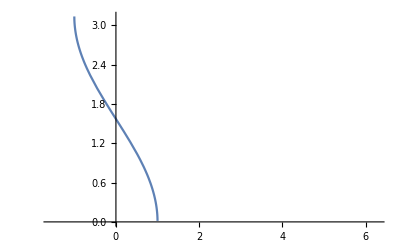

```mathematica
Plot[ArcCos[φ],{φ,-π/2,2π}]
```